```mathematica
α=2.;u0=1.*10^-8;
V[r_]=-1.3862179318475605/r^1.2152447118079408;
k:=√(2e);SPS1={};SPS2={};SPS3={};SPS4={};SPS5={};SPS6={};SPS7={};
```

```mathematica
r2=u0;
```

```mathematica
Print["     ","δ(0.01)→-0.654835316","            ","δ(0.03)→1.232867297","            ","δ(0.07)→-0.579619620","            ","δ(0.1)→-1.156444634","            ","δ(0.3)→-0.106466466","            ","δ(0.7)→-1.457426179","            ","δ(1)→1.160634967","    "];
Table[
e=0.01;
sol1=Flatten@NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs1=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol1,{δ,-1.3},WorkingPrecision->20];
δ1=δ/.δs1;
δ1=NestWhile[Sign[#](Abs[#]-π)&,δ1,Abs[#]>π/2&];
AppendTo[SPS1,{r1,δ1}];
e=0.03;
sol2=Flatten@NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs2=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol2,{δ,0.9},WorkingPrecision->20];
δ2=δ/.δs2;
δ2=NestWhile[Sign[#](Abs[#]-π)&,δ2,Abs[#]>π/2&];
AppendTo[SPS2,{r1,δ2}];
e=0.07;
sol3=Flatten@NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs3=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol3,{δ,-0.2},WorkingPrecision->20];
δ3=δ/.δs3;
δ3=NestWhile[Sign[#](Abs[#]-π)&,δ3,Abs[#]>π/2&];
AppendTo[SPS3,{r1,δ3}];
e=0.1;
sol4=Flatten@NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs4=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol4,{δ,-0.6},WorkingPrecision->20];
δ4=δ/.δs4;
δ4=NestWhile[Sign[#](Abs[#]-π)&,δ4,Abs[#]>π/2&];
AppendTo[SPS4,{r1,δ4}];
e=0.3;
sol5=Flatten@NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs5=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol5,{δ,1.2},WorkingPrecision->20];
δ5=δ/.δs5;
δ5=NestWhile[Sign[#](Abs[#]-π)&,δ5,Abs[#]>π/2&];
AppendTo[SPS5,{r1,δ5}];
e=0.7;
sol6=Flatten@NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs6=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol6,{δ,-0.6},WorkingPrecision->20];
δ6=δ/.δs6;
δ6=NestWhile[Sign[#](Abs[#]-π)&,δ6,Abs[#]>π/2&];
AppendTo[SPS6,{r1,δ6}];
e=1;
sol7=Flatten@NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs7=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol7,{δ,-1.1},WorkingPrecision->20];
δ7=δ/.δs7;
δ7=NestWhile[Sign[#](Abs[#]-π)&,δ7,Abs[#]>π/2&];
AppendTo[SPS7,{r1,δ7}];
Print[r1" ","δ(0.01)→"Style[δ1,If[Abs[δ1+0.65]<0.3,Red,Black]],"  ","δ(0.03)→"Style[δ2,If[Abs[δ2-1.23]<0.3,Red,Black]],"  ","δ(0.07)→"Style[δ3,If[Abs[δ3+0.58]<0.3,Red,Black]],"  ","δ(0.1)→"Style[δ4,If[Abs[δ4+1.15]<0.3,Red,Black]],"  ","δ(0.3)→"Style[δ5,If[Abs[δ5+0.1]<0.3,Red,Black]],"  ","δ(0.7)→"Style[δ6,If[Abs[δ6+1.45]<0.3,Red,Black]],"  ","δ(1)→"Style[δ7,If[Abs[δ7-1.15]<0.3,Red,Black]],"  "],{r1,1,200,1}]
```

δ(0.01)→-0.654835316            δ(0.03)→1.232867297            δ(0.07)→-0.579619620            δ(0.1)→-1.156444634            δ(0.3)→-0.106466466            δ(0.7)→-1.457426179            δ(1)→1.160634967

NDSolve::precw: 参数函数的精度 ({{2. (0.01+1.38622 Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

FindRoot::precw: 参数函数的精度 (34.0524872286675345759775193345717080845991260378==-7.21249 Cot[8.78838-δ]) 小于 WorkingPrecision (20.).

NDSolve::precw: 参数函数的精度 ({{2. (0.03+1.38622 Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

FindRoot::precw: 参数函数的精度 (30.0992227057417373350611040388309919714571848298==-4.32743 Cot[2.66814-δ]) 小于 WorkingPrecision (20.).

NDSolve::precw: 参数函数的精度 ({{2. (0.07+1.38622 Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

FindRoot::precw: 参数函数的精度 (24.5246149391146676571401242900743649904430614331==-3.04678 Cot[0.400649-δ]) 小于 WorkingPrecision (20.).

General::stop: 在本次计算中，FindRoot::precw 的进一步输出将被抑制.

δ(0.01)→ (-0.4276796718180924602)  δ(0.03)→ (-0.330658856537503751)  δ(0.07)→ 0.5242495089595553032  δ(0.1)→ (-0.074116727510864819)  δ(0.3)→ (-1.1746755598169043752)  δ(0.7)→ 1.506872229385686392  δ(1)→ 1.356195216518367612

2  δ(0.01)→ (-1.0733195352442838231)  δ(0.03)→ 1.0045471348688465677  δ(0.07)→ (-0.4384130843024776086)  δ(0.1)→ (-0.79961996276842816339)  δ(0.3)→ (-1.435744652426442292)  δ(0.7)→ 1.454738363927295517  δ(1)→ 1.366701879321742187

3  δ(0.01)→ (-0.57489147263891067637)  δ(0.03)→ (-0.2971262140716686567)  δ(0.07)→ (-1.0621003737497987952)  δ(0.1)→ (-1.2116317580145199086)  δ(0.3)→ (-1.459311114867230402)  δ(0.7)→ 1.479422432207547297  δ(1)→ 1.375619541188314359

4  δ(0.01)→ 1.5393399232754425178  δ(0.03)→ (-0.57767644605089698)  δ(0.07)→ (-1.113262690779870542)  δ(0.1)→ (-1.2282655863868287242)  δ(0.3)→ (-1.490098585323287969)  δ(0.7)→ 1.451114367861240536  δ(1)→ 1.37246745752513564

5  δ(0.01)→ 1.002492465918980397  δ(0.03)→ (-0.83246724509449174247)  δ(0.07)→ (-1.2884194188487872017)  δ(0.1)→ (-1.3840875318025469503)  δ(0.3)→ (-1.57037385568655224)  δ(0.7)→ 1.45245005671910339  δ(1)→ 1.368928602657655125

6  δ(0.01)→ (-0.069764679144269882331)  δ(0.03)→ (-1.353727035435010165)  δ(0.07)→ 1.566600281669954642  δ(0.1)→ 1.544996527949232406  δ(0.3)→ 1.5505506640550300793  δ(0.7)→ 1.432417875867817675  δ(1)→ 1.352851735607871382

7  δ(0.01)→ (-1.0526623470633255938)  δ(0.03)→ 1.3150160866820063691  δ(0.07)→ 1.3604185539058960738  δ(0.1)→ 1.4291342370407972275  δ(0.3)→ 1.5417322223863558493  δ(0.7)→ 1.4140885086425096545  δ(1)→ 1.349014173207352572

8  δ(0.01)→ 1.300007269327502388  δ(0.03)→ 1.0160308522549105404  δ(0.07)→ 1.3015384877529608004  δ(0.1)→ 1.41806411032977562  δ(0.3)→ 1.4887931666186978645  δ(0.7)→ 1.408604529736952012  δ(1)→ 1.328733998302120915

9  δ(0.01)→ 0.82346953133125268798  δ(0.03)→ 0.94028957247469001486  δ(0.07)→ 1.294929615407113649  δ(0.1)→ 1.388754021907194293  δ(0.3)→ 1.4478992208542655931  δ(0.7)→ 1.380935212899140597  δ(1)→ 1.325116849147861447

10  δ(0.01)→ 0.7466429509820193473  δ(0.03)→ 0.91890655867374016917  δ(0.07)→ 1.215225163638727238  δ(0.1)→ 1.290333324111177662  δ(0.3)→ 1.444291401956785161  δ(0.7)→ 1.374913783648538607  δ(1)→ 1.304525856771453437

11  δ(0.01)→ 0.5941000970854804255  δ(0.03)→ 0.77478208029469347058  δ(0.07)→ 1.0753367750801120514  δ(0.1)→ 1.175434470664538342  δ(0.3)→ 1.4213325974707093217  δ(0.7)→ 1.357375189941276923  δ(1)→ 1.300018828489857223

12  δ(0.01)→ 0.205515568131537454  δ(0.03)→ 0.5458568984015469013  δ(0.07)→ 0.93936369686350709174  δ(0.1)→ 1.1032604766200942335  δ(0.3)→ 1.373894440029877176  δ(0.7)→ 1.3375145918685598404  δ(1)→ 1.281557526381637991

13  δ(0.01)→ (-0.25784323992121353129)  δ(0.03)→ 0.30459714069325104859  δ(0.07)→ 0.85734320681770713866  δ(0.1)→ 1.088149859404827015  δ(0.3)→ 1.3517163146795561341  δ(0.7)→ 1.333279296229597176  δ(1)→ 1.274809318126273356

14  δ(0.01)→ (-0.71633062774394254601)  δ(0.03)→ 0.10201813065774785218  δ(0.07)→ 0.8383328430713408004  δ(0.1)→ 1.081630281479593571  δ(0.3)→ 1.3488109477547658069  δ(0.7)→ 1.3088291904934079667  δ(1)→ 1.260051044207166791

15  δ(0.01)→ (-1.1313838747414850929)  δ(0.03)→ (-0.024548677589531839)  δ(0.07)→ 0.8335917767216607234  δ(0.1)→ 1.034902282668778906  δ(0.3)→ 1.3199665583601087558  δ(0.7)→ 1.301112293090960295  δ(1)→ 1.25015363482372199

16  δ(0.01)→ (-1.4695176490002372096)  δ(0.03)→ (-0.0647336226340416148)  δ(0.07)→ 0.789269048394229433  δ(0.1)→ 0.9550713146740349894  δ(0.3)→ 1.28065278552226109  δ(0.7)→ 1.288755632653632914  δ(1)→ 1.239731628251309793

17  δ(0.01)→ 1.452994700488629254  δ(0.03)→ (-0.0672206681006730912)  δ(0.07)→ 0.70289252750844120611  δ(0.1)→ 0.87958308279518228751  δ(0.3)→ 1.2683637816497764275  δ(0.7)→ 1.2685415617591722533  δ(1)→ 1.2266068373422919271

18  δ(0.01)→ 1.379748527156935061  δ(0.03)→ (-0.10628753628740961146)  δ(0.07)→ 0.60491911702690131045  δ(0.1)→ 0.83951277261002139049  δ(0.3)→ 1.2632287356044220692  δ(0.7)→ 1.265633541012170378  δ(1)→ 1.220133145919748051

19  δ(0.01)→ 1.372884188137405488  δ(0.03)→ (-0.20537571850296381275)  δ(0.07)→ 0.5287948574501345017  δ(0.1)→ 0.833539812302180905  δ(0.3)→ 1.2328486543730387156  δ(0.7)→ 1.245725217758379974  δ(1)→ 1.2046215414615895242

20  δ(0.01)→ 1.292700008071838658  δ(0.03)→ (-0.34406095410800165621)  δ(0.07)→ 0.49385375455163713677  δ(0.1)→ 0.8257600369131778722  δ(0.3)→ 1.2007797698856135475  δ(0.7)→ 1.235489126628109191  δ(1)→ 1.200808809092243692

21  δ(0.01)→ 1.113404281333170807  δ(0.03)→ (-0.49352191790623495273)  δ(0.07)→ 0.48981964335971979  δ(0.1)→ 0.7871539517170587805  δ(0.3)→ 1.1937037496763318962  δ(0.7)→ 1.228233953279200147  δ(1)→ 1.1844648078734180163

22  δ(0.01)→ 0.8752553242095306595  δ(0.03)→ (-0.6282727942468287171)  δ(0.07)→ 0.4807138166673806631  δ(0.1)→ 0.72415135409689366633  δ(0.3)→ 1.1863408955762419445  δ(0.7)→ 1.2083709538479310295  δ(1)→ 1.181483613854019762

23  δ(0.01)→ 0.6137276703430819728  δ(0.03)→ (-0.7273207120499370907)  δ(0.07)→ 0.44023498073926421296  δ(0.1)→ 0.6636361270867392425  δ(0.3)→ 1.1564557089403510889  δ(0.7)→ 1.205146690009486857  δ(1)→ 1.166146159062744365

24  δ(0.01)→ 0.3518587451653466797  δ(0.03)→ (-0.7784656430902875239)  δ(0.07)→ 0.37188570115942516686  δ(0.1)→ 0.62926915597249228591  δ(0.3)→ 1.1301383616361894899  δ(0.7)→ 1.190528987605951825  δ(1)→ 1.162138106206026049

25  δ(0.01)→ 0.10640488291710679899  δ(0.03)→ (-0.789524357688403057)  δ(0.07)→ 0.29694648936319574812  δ(0.1)→ 0.62250660075843434648  δ(0.3)→ 1.1258254032171667943  δ(0.7)→ 1.1774850421786528064  δ(1)→ 1.1494073686972915

26  δ(0.01)→ (-0.10715488554918645348)  δ(0.03)→ (-0.7923703303769875841)  δ(0.07)→ 0.23864610431296969904  δ(0.1)→ 0.6185491208298791354  δ(0.3)→ 1.1168299044841651002  δ(0.7)→ 1.173893029938057815  δ(1)→ 1.143007401909399799

27  δ(0.01)→ (-0.27206120788751434207)  δ(0.03)→ (-0.82074403089726134836)  δ(0.07)→ 0.21058254873915874643  δ(0.1)→ 0.5921316325611594431  δ(0.3)→ 1.0882882437497121053  δ(0.7)→ 1.1558469910157533583  δ(1)→ 1.133785948042090359

28  δ(0.01)→ (-0.37261041782389780489)  δ(0.03)→ (-0.88607629865987987213)  δ(0.07)→ 0.20639515194636600836  δ(0.1)→ 0.54263963954627271813  δ(0.3)→ 1.066380387552045804  δ(0.7)→ 1.15054901569573888  δ(1)→ 1.124495572265005836

29  δ(0.01)→ (-0.40763368182911652939)  δ(0.03)→ (-0.97986571533139237753)  δ(0.07)→ 0.20142424385335529308  δ(0.1)→ 0.48916474111751496069  δ(0.3)→ 1.0635471885769841168  δ(0.7)→ 1.141307884640373919  δ(1)→ 1.118735553764227206

30  δ(0.01)→ (-0.409868113506799908)  δ(0.03)→ (-1.086305288192971826)  δ(0.07)→ 0.17406176627283986303  δ(0.1)→ 0.45299178221534327865  δ(0.3)→ 1.0535062537948709737  δ(0.7)→ 1.1262354094551182064  δ(1)→ 1.1070324525185923566

31  δ(0.01)→ (-0.4326708697904579607)  δ(0.03)→ (-1.189132746590058591)  δ(0.07)→ 0.12246818446502902313  δ(0.1)→ 0.4415888722188994943  δ(0.3)→ 1.02659304991507754  δ(0.7)→ 1.124111275717975183  δ(1)→ 1.103769835147614812

32  δ(0.01)→ (-0.5057493484241371934)  δ(0.03)→ (-1.273769353640137909)  δ(0.07)→ 0.060544022335772992935  δ(0.1)→ 0.440458259873856821  δ(0.3)→ 1.0080411412456562145  δ(0.7)→ 1.1094939626208103748  δ(1)→ 1.0909222775480663972

33  δ(0.01)→ (-0.626171665122271995)  δ(0.03)→ (-1.329343206784070624)  δ(0.07)→ 0.0068123309138212920042  δ(0.1)→ 0.4261588303432735429  δ(0.3)→ 1.006009770364475742  δ(0.7)→ 1.10110898634973026  δ(1)→ 1.088589912781274619

34  δ(0.01)→ (-0.77858937702192883022)  δ(0.03)→ (-1.353292911876363248)  δ(0.07)→ (-0.024867552875210460227)  δ(0.1)→ 0.38992433208466329891  δ(0.3)→ 0.99538062592116153261  δ(0.7)→ 1.096326405062207938  δ(1)→ 1.076236897764148328

35  δ(0.01)→ (-0.94801824727058235765)  δ(0.03)→ (-1.35653935426002371)  δ(0.07)→ (-0.033660637808594788257)  δ(0.1)→ 0.34269761401729854576  δ(0.3)→ 0.9701214283900776179  δ(0.7)→ 1.0809097101002773662  δ(1)→ 1.073157996039607096

36  δ(0.01)→ (-1.1224843771187226878)  δ(0.03)→ (-1.3607340784803807427)  δ(0.07)→ (-0.03473629655988545409)  δ(0.1)→ 0.30332969153355320701  δ(0.3)→ 0.95413219342435764782  δ(0.7)→ 1.0779570561524385  δ(1)→ 1.062787875543094327

37  δ(0.01)→ (-1.2921993705028715864)  δ(0.03)→ (-1.3849359531811813694)  δ(0.07)→ (-0.048280277974150486919)  δ(0.1)→ 0.28449072895140946536  δ(0.3)→ 0.95254167299860145157  δ(0.7)→ 1.067796256829240086  δ(1)→ 1.057691815877173131

38  δ(0.01)→ (-1.4482741814389819788)  δ(0.03)→ (-1.435390855687569272)  δ(0.07)→ (-0.08324162817946766067)  δ(0.1)→ 0.28201977927727704  δ(0.3)→ 0.94165412068434336541  δ(0.7)→ 1.0564922779202583567  δ(1)→ 1.050182071827309163

39  δ(0.01)→ 1.559779345900485054  δ(0.03)→ (-1.507004953811438364)  δ(0.07)→ (-0.13350409376504375357)  δ(0.1)→ 0.27712303290359005  δ(0.3)→ 0.91796154497502806274  δ(0.7)→ 1.054306735569902996  δ(1)→ 1.04257772019898534

40  δ(0.01)→ 1.457634281719029478  δ(0.03)→ 1.5521797531585449167  δ(0.07)→ (-0.18479893701486227564)  δ(0.1)→ 0.25454869797111549148  δ(0.3)→ 0.90394377584602101154  δ(0.7)→ 1.0405717588998643915  δ(1)→ 1.037938775093856555

41  δ(0.01)→ 1.393592142071963243  δ(0.03)→ 1.4705228493768498013  δ(0.07)→ (-0.22280368993022924275)  δ(0.1)→ 0.21590046042318339946  δ(0.3)→ 0.90260142538854374594  δ(0.7)→ 1.03511642950382353  δ(1)→ 1.0282293845903546573

42  δ(0.01)→ 1.3668997526634741552  δ(0.03)→ 1.4004657237026384408  δ(0.07)→ (-0.24033559826583204785)  δ(0.1)→ 0.17548028192362668716  δ(0.3)→ 0.89168580926906650255  δ(0.7)→ 1.029347223933150253  δ(1)→ 1.0256307368054471

43  δ(0.01)→ 1.363457196249928169  δ(0.03)→ 1.3506012351478190388  δ(0.07)→ (-0.24286541971324043)  δ(0.1)→ 0.14852764529786492491  δ(0.3)→ 0.86942964739565308435  δ(0.7)→ 1.0164348675617344434  δ(1)→ 1.0149411443371880049

44  δ(0.01)→ 1.358507826217261006  δ(0.03)→ 1.3245755235350548551  δ(0.07)→ (-0.24627932474120888348)  δ(0.1)→ 0.1399426445955606133  δ(0.3)→ 0.85694156514158430195  δ(0.7)→ 1.014541414294298831  δ(1)→ 1.013006875812118791

45  δ(0.01)→ 1.330461720089340653  δ(0.03)→ 1.3177672084778590809  δ(0.07)→ (-0.26483127700533389097)  δ(0.1)→ 0.139122933897180871  δ(0.3)→ 0.8557451482471873614  δ(0.7)→ 1.0041244523772574921  δ(1)→ 1.002787225370413862

46  δ(0.01)→ 1.271048298616104114  δ(0.03)→ 1.317060433417066626  δ(0.07)→ (-0.30113821115878995321)  δ(0.1)→ 0.12890189106182612456  δ(0.3)→ 0.84495964114203054299  δ(0.7)→ 0.995650027924446507  δ(1)→ 1.000059251475681484

47  δ(0.01)→ 1.183174255707593797  δ(0.03)→ 1.3069979205443308134  δ(0.07)→ (-0.34688585165273979383)  δ(0.1)→ 0.10169711121084418879  δ(0.3)→ 0.824000042889731646  δ(0.7)→ 0.9930314072356989471  δ(1)→ 0.9915989798122326303

48  δ(0.01)→ 1.074392793304728054  δ(0.03)→ 1.2780155507826890583  δ(0.07)→ (-0.38918391386743462291)  δ(0.1)→ 0.064545489294982218791  δ(0.3)→ 0.8127087589113537964  δ(0.7)→ 0.98048344511521558527  δ(1)→ 0.9870116352406958563

49  δ(0.01)→ 0.9527951664592180385  δ(0.03)→ 1.2293552428383541512  δ(0.07)→ (-0.41709113930120185168)  δ(0.1)→ 0.031731454319445864369  δ(0.3)→ 0.8116049283546177336  δ(0.7)→ 0.97687557169890398  δ(1)→ 0.9810226161677145427

50  δ(0.01)→ 0.8256590272061414415  δ(0.03)→ 1.1665591236619955492  δ(0.07)→ (-0.4275180383535738149)  δ(0.1)→ 0.014185582976600422598  δ(0.3)→ 0.80105677174527827727  δ(0.7)→ 0.9704083570805365821  δ(1)→ 0.974231405812699312

51  δ(0.01)→ 0.6994161778536958295  δ(0.03)→ 1.097986931807575161  δ(0.07)→ (-0.42837048410365339905)  δ(0.1)→ 0.01088270748453084  δ(0.3)→ 0.78125940276651368914  δ(0.7)→ 0.95967790462110911935  δ(1)→ 0.9706339003261046187

52  δ(0.01)→ 0.5800106555725572589  δ(0.03)→ 1.0325762029506986338  δ(0.07)→ (-0.43396285916861928869)  δ(0.1)→ 0.0086428863316340355  δ(0.3)→ 0.7709113413786320371  δ(0.7)→ 0.9581865258846968097  δ(1)→ 0.96209441794906163573

53  δ(0.01)→ 0.47322913877966530916  δ(0.03)→ 0.97849730275703245863  δ(0.07)→ (-0.45443200310593879911)  δ(0.1)→ (-0.0060475819425335739105)  δ(0.3)→ 0.7698730682219443982  δ(0.7)→ 0.94790024677713791324  δ(1)→ 0.9600714599734631514

54  δ(0.01)→ 0.38473825261132607842  δ(0.03)→ 0.94167995504423333775  δ(0.07)→ (-0.48950256295324540127)  δ(0.1)→ (-0.035130971569505865395)  δ(0.3)→ 0.75963393473698152175  δ(0.7)→ 0.941538133814817057  δ(1)→ 0.95085125669500612783

55  δ(0.01)→ 0.31948213484296143975  δ(0.03)→ 0.92364943776857695978  δ(0.07)→ (-0.53055953649626608433)  δ(0.1)→ (-0.069035273085237524466)  δ(0.3)→ 0.74087629054929244669  δ(0.7)→ 0.938401596818234493  δ(1)→ 0.9491470262749939148

56  δ(0.01)→ 0.2800178399422166171  δ(0.03)→ 0.91953195926927079939  δ(0.07)→ (-0.56621486708818309643)  δ(0.1)→ (-0.094880633414272780744)  δ(0.3)→ 0.7312760031588592337  δ(0.7)→ 0.92710616101869313961  δ(1)→ 0.9405422332989200752

57  δ(0.01)→ 0.263867442288704199  δ(0.03)→ 0.91874350832896787552  δ(0.07)→ (-0.5879074424007263344)  δ(0.1)→ (-0.10580661501852662268)  δ(0.3)→ 0.73029014752425461549  δ(0.7)→ 0.9246609133750349025  δ(1)→ 0.9378978063785906669

58  δ(0.01)→ 0.261653825827942043  δ(0.03)→ 0.90967095696535245149  δ(0.07)→ (-0.5947930508174983091)  δ(0.1)→ (-0.106881235876933924)  δ(0.3)→ 0.72040693772402303209  δ(0.7)→ 0.9177452456699287598  δ(1)→ 0.9309879849575586591

59  δ(0.01)→ 0.259109193531368087  δ(0.03)→ 0.88514036089032224983  δ(0.07)→ (-0.59534314756917413324)  δ(0.1)→ (-0.11151725206541721456)  δ(0.3)→ 0.70258034353304883526  δ(0.7)→ 0.90886286086345687986  δ(1)→ 0.92656300067316494

60  δ(0.01)→ 0.243048530918247101  δ(0.03)→ 0.84439669104799550016  δ(0.07)→ (-0.60208216003051476208)  δ(0.1)→ (-0.12937217156848907165)  δ(0.3)→ 0.6935753865964773217  δ(0.7)→ 0.9074279457472759341  δ(1)→ 0.9218539782809756398

61  δ(0.01)→ 0.206365213081323375  δ(0.03)→ 0.79158341274302728987  δ(0.07)→ (-0.62265344935311138822)  δ(0.1)→ (-0.15857533029189108032)  δ(0.3)→ 0.69263579678248734362  δ(0.7)→ 0.89749532790281042087  δ(1)→ 0.915491513016848509

62  δ(0.01)→ 0.148440653860473957  δ(0.03)→ 0.73333330647088478983  δ(0.07)→ (-0.65557086020192268363)  δ(0.1)→ (-0.18863362868848025)  δ(0.3)→ 0.68313815049483722321  δ(0.7)→ 0.892713793180624809  δ(1)→ 0.9127633684750118174

63  δ(0.01)→ 0.0726528953145252439  δ(0.03)→ 0.67699029221622003968  δ(0.07)→ (-0.69257322717877400022)  δ(0.1)→ (-0.20859583057256951431)  δ(0.3)→ 0.66614770796594747779  δ(0.7)→ 0.8890819276622333359  δ(1)→ 0.90501356220649547074

64  δ(0.01)→ (-0.016081711541655738)  δ(0.03)→ 0.62941257433654394403  δ(0.07)→ (-0.72354639172988656654)  δ(0.1)→ (-0.21508827805790302815)  δ(0.3)→ 0.6576178111797037042  δ(0.7)→ 0.87900398693554975431  δ(1)→ 0.9034199584330601349

65  δ(0.01)→ (-0.11266270807206012664)  δ(0.03)→ 0.59575069260567883106  δ(0.07)→ (-0.74148376396505982632)  δ(0.1)→ (-0.215667082094524179)  δ(0.3)→ 0.65672148820955208828  δ(0.7)→ 0.8772764438670502899  δ(1)→ 0.89532314765838071327

66  δ(0.01)→ (-0.21227780797742669665)  δ(0.03)→ 0.57782097298836370424  δ(0.07)→ (-0.7466155073503563559)  δ(0.1)→ (-0.22275052367866621321)  δ(0.3)→ 0.64762699362345476878  δ(0.7)→ 0.87010800738352855688  δ(1)→ 0.8937017034780685699

67  δ(0.01)→ (-0.310432503491706132)  δ(0.03)→ 0.5725657141887985492  δ(0.07)→ (-0.74716255665790707367)  δ(0.1)→ (-0.24260351757577624012)  δ(0.3)→ 0.63139061575593703477  δ(0.7)→ 0.86277596094379934043  δ(1)→ 0.8864130813145636765

68  δ(0.01)→ (-0.40283490575353976623)  δ(0.03)→ 0.57218304731643556378  δ(0.07)→ (-0.75416486227599131716)  δ(0.1)→ (-0.27088692179755066298)  δ(0.3)→ 0.6232398672944155518  δ(0.7)→ 0.8612145946590297309  δ(1)→ 0.8836942666010285963

69  δ(0.01)→ (-0.48531448968054800155)  δ(0.03)→ 0.56709024896942626308  δ(0.07)→ (-0.77385255892008586388)  δ(0.1)→ (-0.29708161849818551289)  δ(0.3)→ 0.62238485623024541693  δ(0.7)→ 0.85176225098756683192  δ(1)→ 0.8780824579785287671

70  δ(0.01)→ (-0.55392394008944974045)  δ(0.03)→ 0.55016222577027939042  δ(0.07)→ (-0.8043790043988790849)  δ(0.1)→ (-0.3122832548734821251)  δ(0.3)→ 0.6137026647904136396  δ(0.7)→ 0.848165608080403065  δ(1)→ 0.873652778869673183

71  δ(0.01)→ (-0.60539923856048037157)  δ(0.03)→ 0.51913903247310838221  δ(0.07)→ (-0.83806294128770798638)  δ(0.1)→ (-0.31593631831792962313)  δ(0.3)→ 0.59814976719103147627  δ(0.7)→ 0.8440998139743322714  δ(1)→ 0.8700095909424239587

72  δ(0.01)→ (-0.63813370779226456648)  δ(0.03)→ 0.47624136754795537775  δ(0.07)→ (-0.865795669161318073)  δ(0.1)→ (-0.3169322325949702143)  δ(0.3)→ 0.5903009269499422348  δ(0.7)→ 0.83516313439739201781  δ(1)→ 0.86390483215708879252

73  δ(0.01)→ (-0.65355252287698654355)  δ(0.03)→ 0.42645326122462966267  δ(0.07)→ (-0.8815217726421151607)  δ(0.1)→ (-0.32615671249894482319)  δ(0.3)→ 0.58948518400111639703  δ(0.7)→ 0.8338570054968024212  δ(1)→ 0.8618625910379579449

74  δ(0.01)→ (-0.65711119110086133965)  δ(0.03)→ 0.37591035085185059573  δ(0.07)→ (-0.8858368978659278715)  δ(0.1)→ (-0.34710356228863381498)  δ(0.3)→ 0.58121852570473556891  δ(0.7)→ 0.82658524466495717327  δ(1)→ 0.85473017968509125864

75  δ(0.01)→ (-0.6576212015652903123)  δ(0.03)→ 0.33073851256417708435  δ(0.07)→ (-0.88637300319002894655)  δ(0.1)→ (-0.37389727395104136299)  δ(0.3)→ 0.56628865516903448841  δ(0.7)→ 0.820549542269977005  δ(1)→ 0.8534100058579987184

76  δ(0.01)→ (-0.6645000584657924401)  δ(0.03)→ 0.29603253492000307432  δ(0.07)→ (-0.89303308797855296584)  δ(0.1)→ (-0.39648494640284345106)  δ(0.3)→ 0.5586789782766682568  δ(0.7)→ 0.8187679723698712731  δ(1)→ 0.8462615335094501776

77  δ(0.01)→ (-0.6846029513281467214)  δ(0.03)→ 0.274624923882437737  δ(0.07)→ (-0.91131212202230870561)  δ(0.1)→ (-0.40792954190162335653)  δ(0.3)→ 0.55789979998958183826  δ(0.7)→ 0.80986468794042881472  δ(1)→ 0.8445951404976191245

78  δ(0.01)→ (-0.72077622638375235986)  δ(0.03)→ 0.265745904668666812  δ(0.07)→ (-0.93946054125990304184)  δ(0.1)→ (-0.40985989756945939804)  δ(0.3)→ 0.55004773604076733615  δ(0.7)→ 0.807154792767577631  δ(1)→ 0.8384413793934502384

79  δ(0.01)→ (-0.77242851807735377856)  δ(0.03)→ 0.26445968693936683  δ(0.07)→ (-0.97045160489458245154)  δ(0.1)→ (-0.4117044341360743675)  δ(0.3)→ 0.53568926331843772387  δ(0.7)→ 0.8027276754387712608  δ(1)→ 0.835549130579369295

80  δ(0.01)→ (-0.83692378731383180146)  δ(0.03)→ 0.26303587292528977866  δ(0.07)→ (-0.99595842995709106613)  δ(0.1)→ (-0.4226624321608635327)  δ(0.3)→ 0.5282673993264982673  δ(0.7)→ 0.79484124763452083142  δ(1)→ 0.8310469625066890122

81  δ(0.01)→ (-0.91076510204325071036)  δ(0.03)→ 0.25408077455565195627  δ(0.07)→ (-1.010461538780063984)  δ(0.1)→ (-0.44404421626395631251)  δ(0.3)→ 0.52752117203062060487  δ(0.7)→ 0.7937554129759770313  δ(1)→ 0.8265378981852809139

82  δ(0.01)→ (-0.99026883748197380442)  δ(0.03)→ 0.23340406036118089224  δ(0.07)→ (-1.014497020549681246)  δ(0.1)→ (-0.4690728454272450308)  δ(0.3)→ 0.52007981581749064774  δ(0.7)→ 0.78649381540389348132  δ(1)→ 0.8237709700944877733

83  δ(0.01)→ (-1.0718372231095340084)  δ(0.03)→ 0.20088883592026353322  δ(0.07)→ (-1.0149688352608127782)  δ(0.1)→ (-0.48842203597124747927)  δ(0.3)→ 0.50624875239168849878  δ(0.7)→ 0.7815405685446154798  δ(1)→ 0.81786202070711670042

84  δ(0.01)→ (-1.1520123396350318768)  δ(0.03)→ 0.15961325997307793379  δ(0.07)→ (-1.0209117713870611864)  δ(0.1)→ (-0.49694966356255722461)  δ(0.3)→ 0.4989724279496452131  δ(0.7)→ 0.7794958210414825465  δ(1)→ 0.8163282018324284954

85  δ(0.01)→ (-1.2274535975360859869)  δ(0.03)→ 0.11444414691448427734  δ(0.07)→ (-1.0375053260205516619)  δ(0.1)→ (-0.497919303997919519)  δ(0.3)→ 0.49825455285287579762  δ(0.7)→ 0.77117480139433531967  δ(1)→ 0.80974675543291486367

86  δ(0.01)→ (-1.2949412663421772139)  δ(0.03)→ 0.070842995812158007276  δ(0.07)→ (-1.0633601868947629431)  δ(0.1)→ (-0.50077166673742634888)  δ(0.3)→ 0.49121792731732903193  δ(0.7)→ 0.7691238717705029753  δ(1)→ 0.8085518075576365237

87  δ(0.01)→ (-1.351498295638225936)  δ(0.03)→ 0.033917848536292523981  δ(0.07)→ (-1.0921300706091241562)  δ(0.1)→ (-0.51306287138223142381)  δ(0.3)→ 0.47787687599319291828  δ(0.7)→ 0.76440792147244574564  δ(1)→ 0.80226283505429200049

88  δ(0.01)→ (-1.394726880837141807)  δ(0.03)→ 0.007459093298965315  δ(0.07)→ (-1.116108632945756874)  δ(0.1)→ (-0.53441653417192648326)  δ(0.3)→ 0.470711136781382133  δ(0.7)→ 0.7574779833028624659  δ(1)→ 0.8004469557733023973

89  δ(0.01)→ (-1.4234262417909285241)  δ(0.03)→ (-0.0071794395275460268)  δ(0.07)→ (-1.130038967900442591)  δ(0.1)→ (-0.55758502549303066664)  δ(0.3)→ 0.47001605817246589971  δ(0.7)→ 0.7564742440136109469  δ(1)→ 0.7953053415400992747

90  δ(0.01)→ (-1.4384091362731539702)  δ(0.03)→ (-0.012023118605732296)  δ(0.07)→ (-1.13414252033951245)  δ(0.1)→ (-0.57409220328179910496)  δ(0.3)→ 0.46337668445125654269  δ(0.7)→ 0.7493090056733008445  δ(1)→ 0.792183401925834051

91  δ(0.01)→ (-1.443124205658084407)  δ(0.03)→ (-0.012388783395168713)  δ(0.07)→ (-1.134533103039607386)  δ(0.1)→ (-0.58038198622459640911)  δ(0.3)→ 0.45049392940434494996  δ(0.7)→ 0.7452583267729993972  δ(1)→ 0.7886350254094568274

92  δ(0.01)→ (-1.4434369282780018386)  δ(0.03)→ (-0.015141805612767652911)  δ(0.07)→ (-1.1395531199979015122)  δ(0.1)→ (-0.58089997022263159526)  δ(0.3)→ 0.4434097993243523138  δ(0.7)→ 0.7429371790473813234  δ(1)→ 0.78402944749943379227

93  δ(0.01)→ (-1.4462298210020271004)  δ(0.03)→ (-0.026006495565529297711)  δ(0.07)→ (-1.154320778488845038)  δ(0.1)→ (-0.58477126960602954284)  δ(0.3)→ 0.44273108871634160886  δ(0.7)→ 0.73520923699382031955  δ(1)→ 0.7819646343224466948

94  δ(0.01)→ (-1.4574148305130420377)  δ(0.03)→ (-0.047623643508757858326)  δ(0.07)→ (-1.1779674107665223068)  δ(0.1)→ (-0.59804296833260166298)  δ(0.3)→ 0.4364804006187003596  δ(0.7)→ 0.7336410013446985905  δ(1)→ 0.77625160116154409565

95  δ(0.01)→ (-1.4805208346703995623)  δ(0.03)→ (-0.079270225958006359607)  δ(0.07)→ (-1.2048436926503632299)  δ(0.1)→ (-0.6190525318880590099)  δ(0.3)→ 0.42402910789109907884  δ(0.7)→ 0.72870409465492688162  δ(1)→ 0.7750590968149881943

96  δ(0.01)→ (-1.5164636831084058723)  δ(0.03)→ (-0.11774558817907926237)  δ(0.07)→ (-1.227761291309549532)  δ(0.1)→ (-0.64037343376684374828)  δ(0.3)→ 0.4170025627925302004  δ(0.7)→ 0.72263955534954931836  δ(1)→ 0.76901760876013145818

97  δ(0.01)→ (-1.5641705145434119984)  δ(0.03)→ (-0.15852677811803932094)  δ(0.07)→ (-1.241555781642931488)  δ(0.1)→ (-0.65442120967554160459)  δ(0.3)→ 0.4163330228458260151  δ(0.7)→ 0.7216225342169211313  δ(1)→ 0.7678153707786347633

98  δ(0.01)→ 1.52018109062768801  δ(0.03)→ (-0.19675340422555673972)  δ(0.07)→ (-1.245982747056653371)  δ(0.1)→ (-0.65901117976418833091)  δ(0.3)→ 0.41046165111803830761  δ(0.7)→ 0.71461915053065647534  δ(1)→ 0.76233838034569503501

99  δ(0.01)→ 1.456149573422520215  δ(0.03)→ (-0.228076509489334915)  δ(0.07)→ (-1.2463303593748327571)  δ(0.1)→ (-0.65941022233914658252)  δ(0.3)→ 0.39841919084896537955  δ(0.7)→ 0.71131923103795556721  δ(1)→ 0.7602947435256305386

100  δ(0.01)→ 1.388215390703406598  δ(0.03)→ (-0.249556832448144001)  δ(0.07)→ (-1.250344796821127969)  δ(0.1)→ (-0.66423559306820842573)  δ(0.3)→ 0.3914303488360047559  δ(0.7)→ 0.7087261984368161513  δ(1)→ 0.7560681120473364286

101  δ(0.01)→ 1.319247122279870506  δ(0.03)→ (-0.260630085225656412)  δ(0.07)→ (-1.2632264809535952525)  δ(0.1)→ (-0.67819296964761962916)  δ(0.3)→ 0.39076213273090590507  δ(0.7)→ 0.70158776442152078284  δ(1)→ 0.75269616500218714

102  δ(0.01)→ 1.252043795648340824  δ(0.03)→ (-0.263749510571988709)  δ(0.07)→ (-1.284727969024406795)  δ(0.1)→ (-0.69864975406287936983)  δ(0.3)→ 0.3852600944088663842  δ(0.7)→ 0.7003643532211761791  δ(1)→ 0.7499595864477835985

103  δ(0.01)→ 1.189318428713610607  δ(0.03)→ (-0.264002430734970699)  δ(0.07)→ (-1.3099177270441111764)  δ(0.1)→ (-0.7181973602352078735)  δ(0.3)→ 0.37360744623206919045  δ(0.7)→ 0.69526819194528951504  δ(1)→ 0.74528025035452341309

104  δ(0.01)→ 1.133650334286679578  δ(0.03)→ (-0.26739820724029717963)  δ(0.07)→ (-1.332072287869394179)  δ(0.1)→ (-0.73013549153256550167)  δ(0.3)→ 0.3666399449026469676  δ(0.7)→ 0.68998294529716010555  δ(1)→ 0.7437530411908096211

105  δ(0.01)→ 1.08734503908617519  δ(0.03)→ (-0.27862223760990417882)  δ(0.07)→ (-1.346024727874052116)  δ(0.1)→ (-0.73344667438378894325)  δ(0.3)→ 0.36596467146270685536  δ(0.7)→ 0.6888871582808935082  δ(1)→ 0.73827240463441915543

106  δ(0.01)→ 1.0521458079762512237  δ(0.03)→ (-0.29958634074427740603)  δ(0.07)→ (-1.350980602321911378)  δ(0.1)→ (-0.73393823302584542608)  δ(0.3)→ 0.36082150556210369156  δ(0.7)→ 0.68209527062830161577  δ(1)→ 0.7372670180379489793

107  δ(0.01)→ 1.0287768701508298335  δ(0.03)→ (-0.32933172037642243392)  δ(0.07)→ (-1.351375698902478971)  δ(0.1)→ (-0.7396179640211794369)  δ(0.3)→ 0.34954274680418919761  δ(0.7)→ 0.679417358734440435  δ(1)→ 0.73178143450567175115

108  δ(0.01)→ 1.0164055511373204322  δ(0.03)→ (-0.36481521907992998193)  δ(0.07)→ (-1.3543942736960216648)  δ(0.1)→ (-0.75402184202050137022)  δ(0.3)→ 0.342583240264977772  δ(0.7)→ 0.6765675839880042586  δ(1)→ 0.7304600335344693985

109  δ(0.01)→ 1.012286714888836297  δ(0.03)→ (-0.40189423648519909421)  δ(0.07)→ (-1.3653838831920751478)  δ(0.1)→ (-0.77379421558987803222)  δ(0.3)→ 0.34189211426940586738  δ(0.7)→ 0.67000572207392671062  δ(1)→ 0.72576310022366149224

110  δ(0.01)→ 1.01196079971654662  δ(0.03)→ (-0.4361938562774293297)  δ(0.07)→ (-1.3847788606884539621)  δ(0.1)→ (-0.79167584271073053803)  δ(0.3)→ 0.33709696246606119138  δ(0.7)→ 0.6690183969990144921  δ(1)→ 0.7234416361126557321

111  δ(0.01)→ 1.010177211455987884  δ(0.03)→ (-0.4638889412336316479)  δ(0.07)→ (-1.4083934906558400308)  δ(0.1)→ (-0.80181438384776855303)  δ(0.3)→ 0.32617882474014795799  δ(0.7)→ 0.66381823362544738959  δ(1)→ 0.7200396841497544619

112  δ(0.01)→ 1.002211093607585995  δ(0.03)→ (-0.4825281989498341849)  δ(0.07)→ (-1.429955458261098782)  δ(0.1)→ (-0.8041736464162490126)  δ(0.3)→ 0.319216583278284713  δ(0.7)→ 0.65923197603378136575  δ(1)→ 0.7164288587028770592

113  δ(0.01)→ 0.9849076618368029128  δ(0.03)→ (-0.491865582721318684)  δ(0.07)→ (-1.444255784049234855)  δ(0.1)→ (-0.80488662150108139293)  δ(0.3)→ 0.31850050457209539046  δ(0.7)→ 0.6580132755946608442  δ(1)→ 0.7143661194629147574

114  δ(0.01)→ 0.957021810611788568  δ(0.03)→ (-0.494331418413354614)  δ(0.07)→ (-1.449912588286395147)  δ(0.1)→ (-0.81130912796412857716)  δ(0.3)→ 0.31404217005558505036  δ(0.7)→ 0.65147023585843406064  δ(1)→ 0.70966416696720630379

115  δ(0.01)→ 0.9189386597018085553  δ(0.03)→ (-0.494578555370219378)  δ(0.07)→ (-1.4504874507655811224)  δ(0.1)→ (-0.82596913765995645574)  δ(0.3)→ 0.30347365514024991962  δ(0.7)→ 0.649304540875243439  δ(1)→ 0.7085178009370191073

116  δ(0.01)→ 0.8721368052001932239  δ(0.03)→ (-0.49794033975137617802)  δ(0.07)→ (-1.4525918553916043008)  δ(0.1)→ (-0.84498021275328245632)  δ(0.3)→ 0.296500242282945051  δ(0.7)→ 0.64621945800804670089  δ(1)→ 0.70332587314193328448

117  δ(0.01)→ 0.8186913795749956415  δ(0.03)→ (-0.5085151445149127398)  δ(0.07)→ (-1.4617263169479597194)  δ(0.1)→ (-0.86131836609813854824)  δ(0.3)→ 0.29574990898457736485  δ(0.7)→ 0.64021508525044258648  δ(1)→ 0.7023692501358801021

118  δ(0.01)→ 0.7609349378841411709  δ(0.03)→ (-0.52795060245837955266)  δ(0.07)→ (-1.4790358113830622459)  δ(0.1)→ (-0.86992710763255398275)  δ(0.3)→ 0.2916168864142387841  δ(0.7)→ 0.6393776017463176453  δ(1)→ 0.69746452044922089762

119  δ(0.01)→ 0.7012705604014184596  δ(0.03)→ (-0.55535637732930590343)  δ(0.07)→ (-1.5011136145413034769)  δ(0.1)→ (-0.871586845683417101)  δ(0.3)→ 0.28138892483557930314  δ(0.7)→ 0.63412248411463657979  δ(1)→ 0.6959363363993821411

120  δ(0.01)→ 0.6420859379158951361  δ(0.03)→ (-0.58796898059026900824)  δ(0.07)→ (-1.522155243338733042)  δ(0.1)→ (-0.87259442604890160428)  δ(0.3)→ 0.274397940225766008  δ(0.7)→ 0.6301608192634028589  δ(1)→ 0.6919876413623921521

121  δ(0.01)→ 0.5857131766320324287  δ(0.03)→ (-0.6220149360263812354)  δ(0.07)→ (-1.536911757520628788)  δ(0.1)→ (-0.87964866862580818866)  δ(0.3)→ 0.273603944743397502  δ(0.7)→ 0.6287905796848650068  δ(1)→ 0.689367134338682467

122  δ(0.01)→ 0.53438565393531965507  δ(0.03)→ (-0.6535014601404707686)  δ(0.07)→ (-1.543411814241194396)  δ(0.1)→ (-0.89441538533211280653)  δ(0.3)→ 0.26978444107260481303  δ(0.7)→ 0.62252406980412621009  δ(1)→ 0.6866962479050088426

123  δ(0.01)→ 0.49014785077561572543  δ(0.03)→ (-0.6789446992066610454)  δ(0.07)→ (-1.54432781286576349)  δ(0.1)→ (-0.91262680149077379183)  δ(0.3)→ 0.25988960221286418344  δ(0.7)→ 0.6207765215493799373  δ(1)→ 0.68288479315937713506

124  δ(0.01)→ 0.45467816394096133958  δ(0.03)→ (-0.6961237972107633316)  δ(0.07)→ (-1.5456571924423569632)  δ(0.1)→ (-0.92754826410410329131)  δ(0.3)→ 0.252876452682873839  δ(0.7)→ 0.61748114281902512737  δ(1)→ 0.6813579863904953443

125  δ(0.01)→ 0.42900096286581660788  δ(0.03)→ (-0.7048144610412678438)  δ(0.07)→ (-1.5530130832947666821)  δ(0.1)→ (-0.93485923599521202223)  δ(0.3)→ 0.252029377588843374  δ(0.7)→ 0.61201112411709463415  δ(1)→ 0.67670373391684721753

126  δ(0.01)→ 0.41311341781566202621  δ(0.03)→ (-0.707185867618375659)  δ(0.07)→ (-1.5682510002086454438)  δ(0.1)→ (-0.936013538711812435)  δ(0.3)→ 0.24851132473319113433  δ(0.7)→ 0.6112548728720777954  δ(1)→ 0.6757902400601980593

127  δ(0.01)→ 0.40564635143630934375  δ(0.03)→ (-0.7073971546168704888)  δ(0.07)→ 1.552815500815841464  δ(0.1)→ (-0.93735170430867428661)  δ(0.3)→ 0.23894354857606618951  δ(0.7)→ 0.60598811298374804814  δ(1)→ 0.6709510279887335218

128  δ(0.01)→ 0.403776642348781042  δ(0.03)→ (-0.71026446483902421453)  δ(0.07)→ 1.5322986492545867699  δ(0.1)→ (-0.94493352519312237788)  δ(0.3)→ 0.231905272606878631  δ(0.7)→ 0.6025823482763734606  δ(1)→ 0.6699239948745289172

129  δ(0.01)→ 0.40359560273286771  δ(0.03)→ (-0.71958305012413418757)  δ(0.07)→ 1.5170461570107166761  δ(0.1)→ (-0.95969103036098702185)  δ(0.3)→ 0.23099576666601013654  δ(0.7)→ 0.6010434078196618296  δ(1)→ 0.66562195487861325438

130  δ(0.01)→ 0.400918990049261328  δ(0.03)→ (-0.73700462428615336354)  δ(0.07)→ 1.5095922639210462595  δ(0.1)→ (-0.97709125462450854438)  δ(0.3)→ 0.22776683142343147891  δ(0.7)→ 0.59507338776884650124  δ(1)→ 0.6638261273440949059

131  δ(0.01)→ 0.3922192020386773059  δ(0.03)→ (-0.76187817985549847885)  δ(0.07)→ 1.5081580577575464753  δ(0.1)→ (-0.99072057613225750531)  δ(0.3)→ 0.21852120223852841317  δ(0.7)→ 0.593663042758588433  δ(1)→ 0.6605847221420898038

132  δ(0.01)→ 0.3752647580403935071  δ(0.03)→ (-0.7917862301227654824)  δ(0.07)→ 1.507418865933397612  δ(0.1)→ (-0.99693186306377943773)  δ(0.3)→ 0.211456305554251535  δ(0.7)→ 0.590184226185826448  δ(1)→ 0.65767206724336415395

133  δ(0.01)→ 0.3492721115256287146  δ(0.03)→ (-0.8233102198994521849)  δ(0.07)→ 1.501725542374512123  δ(0.1)→ (-0.9977294393228161573)  δ(0.3)→ 0.21047517204231147555  δ(0.7)→ 0.58522279058537632744  δ(1)→ 0.6556306156545044901

134  δ(0.01)→ 0.3146743908041936013  δ(0.03)→ (-0.8527648962109047426)  δ(0.07)→ 1.488540886991381621  δ(0.1)→ (-0.99940965392971478942)  δ(0.3)→ 0.20752275877035217953  δ(0.7)→ 0.584493202004659852  δ(1)→ 0.65167898812497850129

135  δ(0.01)→ 0.272739397746004849  δ(0.03)→ (-0.8768815916316936818)  δ(0.07)→ 1.469616534866854788  δ(0.1)→ (-1.007424641431782252)  δ(0.3)→ 0.19859529848758773632  δ(0.7)→ 0.57925287793548714768  δ(1)→ 0.650550152838718988

136  δ(0.01)→ 0.225216713465591694  δ(0.03)→ (-0.8935022747176423794)  δ(0.07)→ 1.4496886588024901892  δ(0.1)→ (-1.0220840456136716694)  δ(0.3)→ 0.19150362481479204  δ(0.7)→ 0.57633966286549498  δ(1)→ 0.64602478611671350869

137  δ(0.01)→ 0.174087424049162066  δ(0.03)→ (-0.9022463153725239545)  δ(0.07)→ 1.4339603180031577262  δ(0.1)→ (-1.0386799525652554625)  δ(0.3)→ 0.190441887451298054  δ(0.7)→ 0.5746234396124924481  δ(1)→ 0.6452078558878683992

138  δ(0.01)→ 0.12141533373505682897  δ(0.03)→ (-0.9048925806496445011)  δ(0.07)→ 1.4254780299410422213  δ(0.1)→ (-1.0511357372433687045)  δ(0.3)→ 0.18775313928162239009  δ(0.7)→ 0.56896363889439904867  δ(1)→ 0.64078347494510136717

139  δ(0.01)→ 0.069267575955501584202  δ(0.03)→ (-0.90508558552917111999)  δ(0.07)→ 1.423346185612220049  δ(0.1)→ (-1.056415655272666484)  δ(0.3)→ 0.17914062134834958987  δ(0.7)→ 0.567820626083573992  δ(1)→ 0.6395893755843157292

140  δ(0.01)→ 0.019666748371748089317  δ(0.03)→ (-0.90722097291645861218)  δ(0.07)→ 1.422977599952763129  δ(0.1)→ (-1.0569700164071599404)  δ(0.3)→ 0.172023236855415906  δ(0.7)→ 0.56418594252727076838  δ(1)→ 0.6359004289263568215

141  δ(0.01)→ (-0.025460993159323890846)  δ(0.03)→ (-0.9149523534580275077)  δ(0.07)→ 1.418791086602926329  δ(0.1)→ (-1.0589879168043588247)  δ(0.3)→ 0.1708722076835062651  δ(0.7)→ 0.55970565081219454692  δ(1)→ 0.6338042065190819708

142  δ(0.01)→ (-0.064374473538271042862)  δ(0.03)→ (-0.93009104561160987462)  δ(0.07)→ 1.40762575840716735  δ(0.1)→ (-1.0673523215367349737)  δ(0.3)→ 0.16843402009144145445  δ(0.7)→ 0.5589594766525009894  δ(1)→ 0.6312149804133975387

143  δ(0.01)→ (-0.095670402032006020467)  δ(0.03)→ (-0.95233181698360282141)  δ(0.07)→ 1.390372543049164435  δ(0.1)→ (-1.0818463402735152948)  δ(0.3)→ 0.16013380991713181106  δ(0.7)→ 0.55377891938995518519  δ(1)→ 0.628043020741230296

144  δ(0.01)→ (-0.11851333934219284667)  δ(0.03)→ (-0.9796513969591046569)  δ(0.07)→ 1.3711431703582645796  δ(0.1)→ (-1.0976571760596494198)  δ(0.3)→ 0.152992888668662288  δ(0.7)→ 0.551299865381127825  δ(1)→ 0.6265204437518257011

145  δ(0.01)→ (-0.1329181090871003322)  δ(0.03)→ (-1.008983791918367343)  δ(0.07)→ 1.3550123118014002732  δ(0.1)→ (-1.1090501311796250878)  δ(0.3)→ 0.151744235116136568  δ(0.7)→ 0.5494042694573102857  δ(1)→ 0.6225056286187580043

146  δ(0.01)→ (-0.13999662831575729777)  δ(0.03)→ (-1.036907969564717548)  δ(0.07)→ 1.3454676320479082889  δ(0.1)→ (-1.113541303211123814)  δ(0.3)→ 0.14954325669946844635  δ(0.7)→ 0.54406329572916656232  δ(1)→ 0.6216391456083514359

147  δ(0.01)→ (-0.142019845648480121)  δ(0.03)→ (-1.060293911588806919)  δ(0.07)→ 1.342469203111667538  δ(0.1)→ (-1.1139387076326628116)  δ(0.3)→ 0.14155315790942226794  δ(0.7)→ 0.5431271788539460082  δ(1)→ 0.61732694779194977212

148  δ(0.01)→ (-0.142156278528315844)  δ(0.03)→ (-1.07694737462599741)  δ(0.07)→ 1.342228102770381765  δ(0.1)→ (-1.1162800326166597396)  δ(0.3)→ 0.134391895731866745  δ(0.7)→ 0.53936416007171148903  δ(1)→ 0.6164857135215692197

149  δ(0.01)→ (-0.143886469654142929)  δ(0.03)→ (-1.086230721631588185)  δ(0.07)→ 1.339353584975560286  δ(0.1)→ (-1.1249206326524913681)  δ(0.3)→ 0.13303769557996121759  δ(0.7)→ 0.53533657863874497141  δ(1)→ 0.61252871548838879404

150  δ(0.01)→ (-0.150292684510293769)  δ(0.03)→ (-1.089460383676237377)  δ(0.07)→ 1.330148009012259044  δ(0.1)→ (-1.1391991483954864231)  δ(0.3)→ 0.13106034218159090146  δ(0.7)→ 0.5345398121535701267  δ(1)→ 0.6110962035420358631

151  δ(0.01)→ (-0.163511244546324587)  δ(0.03)→ (-1.08974741182255924)  δ(0.07)→ 1.31463962934824257  δ(0.1)→ (-1.1542522055226292138)  δ(0.3)→ 0.12337847188505679785  δ(0.7)→ 0.52944805563601622951  δ(1)→ 0.6080139354054228571

152  δ(0.01)→ (-0.184521868154829284)  δ(0.03)→ (-1.0911039622831996888)  δ(0.07)→ 1.2962504342834558854  δ(0.1)→ (-1.1646843026746302529)  δ(0.3)→ 0.116200985928201525  δ(0.7)→ 0.527349354092639656  δ(1)→ 0.605612607622045865

153  δ(0.01)→ (-0.213247660085642866)  δ(0.03)→ (-1.0971155198752553438)  δ(0.07)→ 1.2798372243822159226  δ(0.1)→ (-1.16850738571576289)  δ(0.3)→ 0.11473378514596591  δ(0.7)→ 0.52527722054365807099  δ(1)→ 0.6036045031795370299

154  δ(0.01)→ (-0.248818827489296471)  δ(0.03)→ (-1.1098360578896141417)  δ(0.07)→ 1.2692403315353314018  δ(0.1)→ (-1.168813015421428923)  δ(0.3)→ 0.1129662552005630901  δ(0.7)→ 0.52025945866263382823  δ(1)→ 0.60022847469993429102

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法找到 merit 函数的充足的降低. 您可能需要多于 20. 位工作精度以满足这些容差.

155  δ(0.01)→ (-0.28985708527114562508)  δ(0.03)→ (-1.1293761203868413981)  δ(0.07)→ 1.265228755091796054  δ(0.1)→ (-1.1714576250750504677)  δ(0.3)→ 0.10559091557469248126  δ(0.7)→ 0.5194779004584649252  δ(1)→ 0.5991070265163053141

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法找到 merit 函数的充足的降低. 您可能需要多于 20. 位工作精度以满足这些容差.

156  δ(0.01)→ (-0.33470263974916278031)  δ(0.03)→ (-1.154150284614509737)  δ(0.07)→ 1.26486036350297093  δ(0.1)→ (-1.1803110555364750248)  δ(0.3)→ 0.0984021768630234087  δ(0.7)→ 0.51561354174649864968  δ(1)→ 0.5951162508676559219

157  δ(0.01)→ (-0.38156585269830772569)  δ(0.03)→ (-1.181458355459701656)  δ(0.07)→ 1.263066636378158282  δ(0.1)→ (-1.1943375335159245342)  δ(0.3)→ 0.096815034109968633  δ(0.7)→ 0.51200972489022549995  δ(1)→ 0.5943827744105448393

158  δ(0.01)→ (-0.4286185741922823816)  δ(0.03)→ (-1.208128812755086612)  δ(0.07)→ 1.255727412408777177  δ(0.1)→ (-1.2086650648426516432)  δ(0.3)→ 0.095243321572350764044  δ(0.7)→ 0.5111359854024106875  δ(1)→ 0.59036390848631973269

159  δ(0.01)→ (-0.4740514748457033832)  δ(0.03)→ (-1.231133933348044692)  δ(0.07)→ 1.242028302097459925  δ(0.1)→ (-1.2182293773466418838)  δ(0.3)→ 0.088172898126292561497  δ(0.7)→ 0.50615817020961045785  δ(1)→ 0.5893968742277260241

160  δ(0.01)→ (-0.51612499147385178091)  δ(0.03)→ (-1.248194816589937254)  δ(0.07)→ 1.2246404618609355604  δ(0.1)→ (-1.22148637616289887)  δ(0.3)→ 0.080978644197498021  δ(0.7)→ 0.504390231537229755  δ(1)→ 0.58594430546356767589

161  δ(0.01)→ (-0.55323981369544353908)  δ(0.03)→ (-1.258368400834876005)  δ(0.07)→ 1.2081050471597222354  δ(0.1)→ (-1.221749114589914227)  δ(0.3)→ 0.079265175325520687  δ(0.7)→ 0.50214815738689628202  δ(1)→ 0.5842291778741453529

162  δ(0.01)→ (-0.58404937507101716078)  δ(0.03)→ (-1.26247077899242186)  δ(0.07)→ 1.1965122947241005683  δ(0.1)→ (-1.2246737173778110473)  δ(0.3)→ 0.077875096987453803319  δ(0.7)→ 0.49745445829964979789  δ(1)→ 0.5817274248341196716

163  δ(0.01)→ (-0.60762764233521355621)  δ(0.03)→ (-1.263055975299647)  δ(0.07)→ 1.1913738733746794891  δ(0.1)→ (-1.2336855490696652527)  δ(0.3)→ 0.071107958032614686629  δ(0.7)→ 0.496782148611284889  δ(1)→ 0.5790428212180441107

164  δ(0.01)→ (-0.62368338406738565619)  δ(0.03)→ (-1.2637433046327785842)  δ(0.07)→ 1.190624265364631679  δ(0.1)→ (-1.2474341610054380649)  δ(0.3)→ 0.063914622466805032  δ(0.7)→ 0.49284256715003036997  δ(1)→ 0.5775295507029445873

165  δ(0.01)→ (-0.6327723745108690224)  δ(0.03)→ (-1.2680582336276924799)  δ(0.07)→ 1.189648866391977078  δ(0.1)→ (-1.2610711924738896748)  δ(0.3)→ 0.062069046607431145  δ(0.7)→ 0.48963341130524597812  δ(1)→ 0.57402233182848701511

166  δ(0.01)→ (-0.6364123284404645713)  δ(0.03)→ (-1.2783262922318921147)  δ(0.07)→ 1.184042978407245692  δ(0.1)→ (-1.2698521401306838699)  δ(0.3)→ 0.060846259106531232067  δ(0.7)→ 0.4886626570412358544  δ(1)→ 0.5731806918468848195

167  δ(0.01)→ (-0.636988908029844522)  δ(0.03)→ (-1.295116859255151685)  δ(0.07)→ 1.172195965237642851  δ(0.1)→ (-1.272629271969377295)  δ(0.3)→ 0.054380670807031682472  δ(0.7)→ 0.48382037094309376735  δ(1)→ 0.56930476611095704189

168  δ(0.01)→ (-0.637400728747417085)  δ(0.03)→ (-1.317324326364358572)  δ(0.07)→ 1.1559777214409238664  δ(0.1)→ (-1.2728854153424233046)  δ(0.3)→ 0.0471953089226714861  δ(0.7)→ 0.482337519690050178  δ(1)→ 0.5685858749091624996

169  δ(0.01)→ (-0.6405226185383532747)  δ(0.03)→ (-1.342642166518896594)  δ(0.07)→ 1.1395124568236348306  δ(0.1)→ (-1.2760653754411354133)  δ(0.3)→ 0.045212481676148442  δ(0.7)→ 0.47993496332962660044  δ(1)→ 0.564929933928295947

170  δ(0.01)→ (-0.6486793413864449897)  δ(0.03)→ (-1.36815796988796627)  δ(0.07)→ 1.1270263791372334368  δ(0.1)→ (-1.2851891327811137868)  δ(0.3)→ 0.044142513683751460096  δ(0.7)→ 0.47556319915304424416  δ(1)→ 0.563758462386992767

171  δ(0.01)→ (-0.66331535527458517982)  δ(0.03)→ (-1.390941531108594735)  δ(0.07)→ 1.1206888780357995463  δ(0.1)→ (-1.2986424623911035337)  δ(0.3)→ 0.03797656000659917083  δ(0.7)→ 0.4749609731886181997  δ(1)→ 0.56082767710371267268

172  δ(0.01)→ (-0.68492629279470582317)  δ(0.03)→ (-1.408618126370286818)  δ(0.07)→ 1.119317720671437972  δ(0.1)→ (-1.3116252480701568952)  δ(0.3)→ 0.030806782944000998  δ(0.7)→ 0.47097116817008189381  δ(1)→ 0.558813425978203349

173  δ(0.01)→ (-0.71319070907600497786)  δ(0.03)→ (-1.419928219559020156)  δ(0.07)→ 1.11887464793051406  δ(0.1)→ (-1.319699066166775245)  δ(0.3)→ 0.028682230350305649  δ(0.7)→ 0.468127681878726052  δ(1)→ 0.5568455885755976302

174  δ(0.01)→ (-0.74718944254249736274)  δ(0.03)→ (-1.42517513208623038)  δ(0.07)→ 1.114826538095261166  δ(0.1)→ (-1.322069234244673942)  δ(0.3)→ 0.027750507969622253628  δ(0.7)→ 0.4670451833140337373  δ(1)→ 0.55392311811809858989

175  δ(0.01)→ (-0.78562143364602581153)  δ(0.03)→ (-1.426332057690640127)  δ(0.07)→ 1.10484205606695124  δ(0.1)→ (-1.3223453536445384983)  δ(0.3)→ 0.021882025085847294116  δ(0.7)→ 0.46235679398103406138  δ(1)→ 0.5528058860914224981

176  δ(0.01)→ (-0.82697190077426565444)  δ(0.03)→ (-1.4265854150266427423)  δ(0.07)→ 1.0899564267092040013  δ(0.1)→ (-1.3257558884792935824)  δ(0.3)→ 0.014735925256206169  δ(0.7)→ 0.461116966970829058  δ(1)→ 0.54925228591448489723

177  δ(0.01)→ (-0.86962659045748440001)  δ(0.03)→ (-1.4293594379235185271)  δ(0.07)→ 1.0737770382968520473  δ(0.1)→ (-1.3349520707322747258)  δ(0.3)→ 0.012465871103325734  δ(0.7)→ 0.45856554343135240417  δ(1)→ 0.5485703452600123956

178  δ(0.01)→ (-0.91194565489477157007)  δ(0.03)→ (-1.4372341406970869426)  δ(0.07)→ 1.0605441946905287643  δ(0.1)→ (-1.3480992924800444397)  δ(0.3)→ 0.011657765200329927288  δ(0.7)→ 0.45451107246155357783  δ(1)→ 0.54489702873527755673

179  δ(0.01)→ (-0.95231765761652427745)  δ(0.03)→ (-1.451254476808386895)  δ(0.07)→ 1.0529831601702505566  δ(0.1)→ (-1.3604642387003312924)  δ(0.3)→ 0.0060842670748310931715  δ(0.7)→ 0.4539451698881551113  δ(1)→ 0.544089945460207386

180  δ(0.01)→ (-0.98921508411170173706)  δ(0.03)→ (-1.470832334530679969)  δ(0.07)→ 1.0507760871409588453  δ(0.1)→ (-1.367899567858325049)  δ(0.3)→ (-0.001029640452928882)  δ(0.7)→ 0.44992887942274732906  δ(1)→ 0.54085057639592748607

181  δ(0.01)→ (-1.0212711488304925891)  δ(0.03)→ (-1.494093936115822401)  δ(0.07)→ 1.050565893698956615  δ(0.1)→ (-1.369924444556240752)  δ(0.3)→ (-0.003448247973233729)  δ(0.7)→ 0.44742237899159669139  δ(1)→ 0.5394214160223034935

182  δ(0.01)→ (-1.0473933271473919942)  δ(0.03)→ (-1.518415343747335803)  δ(0.07)→ 1.047857761626976977  δ(0.1)→ (-1.3702396072273853369)  δ(0.3)→ (-0.0041474036602700358073)  δ(0.7)→ 0.4462178957567662479  δ(1)→ 0.537007704003354714

183  δ(0.01)→ (-1.0669183306207226996)  δ(0.03)→ (-1.540983704319841136)  δ(0.07)→ 1.039705019566094505  δ(0.1)→ (-1.3738565551390921879)  δ(0.3)→ (-0.0094287674428886544105)  δ(0.7)→ 0.44169879593140613597  δ(1)→ 0.534704628596172014

184  δ(0.01)→ (-1.0797915388995452184)  δ(0.03)→ (-1.559345048233498825)  δ(0.07)→ 1.0262977945062712498  δ(0.1)→ (-1.3830917414482500634)  δ(0.3)→ (-0.01650161667499567)  δ(0.7)→ 0.44066331930937022  δ(1)→ 0.5332049379256650586

185  δ(0.01)→ (-1.0867212068865801046)  δ(0.03)→ 1.5696522306667452659  δ(0.07)→ 1.0106335069516039903  δ(0.1)→ (-1.3959271586684108796)  δ(0.3)→ (-0.019071091429825441)  δ(0.7)→ 0.43797624631398076328  δ(1)→ 0.53010933071082705529

186  δ(0.01)→ (-1.0892277315327163064)  δ(0.03)→ 1.5630223312158594897  δ(0.07)→ 0.99684017196601209538  δ(0.1)→ (-1.4077100859947769155)  δ(0.3)→ (-0.019675946314167193734)  δ(0.7)→ 0.43423228487939719102  δ(1)→ 0.5292810495476526901

187  δ(0.01)→ (-1.0895108198963936)  δ(0.03)→ 1.5609818209059405073  δ(0.07)→ 0.9880826812967448627  δ(0.1)→ (-1.414568611271432768)  δ(0.3)→ (-0.024668441898741101331)  δ(0.7)→ 0.4336737428349707317  δ(1)→ 0.52577150673446980117

188  δ(0.01)→ (-1.090117897766992885)  δ(0.03)→ 1.560832111247482405  δ(0.07)→ 0.9848626002520069278  δ(0.1)→ (-1.41630040661209878)  δ(0.3)→ (-0.0316910763525963186)  δ(0.7)→ 0.42965332490558969267  δ(1)→ 0.5251357179087268461

189  δ(0.01)→ (-1.0934967243099561838)  δ(0.03)→ 1.559326726550138516  δ(0.07)→ 0.984584362690483821  δ(0.1)→ (-1.4166679060296441901)  δ(0.3)→ (-0.034412972993284051)  δ(0.7)→ 0.427455590526327636  δ(1)→ 0.52174348900491572115

190  δ(0.01)→ (-1.1015836757905563673)  δ(0.03)→ 1.553689492623122356  δ(0.07)→ 0.9829598722229455036  δ(0.1)→ (-1.4204681958242343349)  δ(0.3)→ (-0.034938126391297055396)  δ(0.7)→ 0.42612268829005161964  δ(1)→ 0.5207653017600771537

191  δ(0.01)→ (-1.1155575895271334223)  δ(0.03)→ 1.5424128525861593729  δ(0.07)→ 0.9765604504439332152  δ(0.1)→ (-1.4297142163087245351)  δ(0.3)→ (-0.039645482266181783003)  δ(0.7)→ 0.42178555910528526844  δ(1)→ 0.51797615250493218348

192  δ(0.01)→ (-1.1357966653307204178)  δ(0.03)→ 1.5255400011145679774  δ(0.07)→ 0.96474879404309939297  δ(0.1)→ (-1.4422361136442068355)  δ(0.3)→ (-0.0466085298488951015)  δ(0.7)→ 0.4209189032739640653  δ(1)→ 0.516262722816172996

193  δ(0.01)→ (-1.1619874723604376134)  δ(0.03)→ 1.5044668848747681909  δ(0.07)→ 0.94983158754607640091  δ(0.1)→ (-1.4534717649177983932)  δ(0.3)→ (-0.0494836225218670378)  δ(0.7)→ 0.41811055403889996178  δ(1)→ 0.5143387528993504384

194  δ(0.01)→ (-1.193301642942604374)  δ(0.03)→ 1.4814844214383899314  δ(0.07)→ 0.93569740304800164765  δ(0.1)→ (-1.45980885123803187)  δ(0.3)→ (-0.049943582555752078438)  δ(0.7)→ 0.41466850705649943786  δ(1)→ 0.511781591018014972

195  δ(0.01)→ (-1.2285720288768816474)  δ(0.03)→ 1.4592490901069593362  δ(0.07)→ 0.9258230943426518552  δ(0.1)→ (-1.46129180371108773)  δ(0.3)→ (-0.054370014770585038811)  δ(0.7)→ 0.4140926350095657613  δ(1)→ 0.5106681050614361228

196  δ(0.01)→ (-1.2664340680484722441)  δ(0.03)→ 1.440256624241391258  δ(0.07)→ 0.92145975093858054051  δ(0.1)→ (-1.4617204896154489242)  δ(0.3)→ (-0.0612639390575341106)  δ(0.7)→ 0.41008899867748477878  δ(1)→ 0.50747806652916614472

197  δ(0.01)→ (-1.3054262781570918603)  δ(0.03)→ 1.4263266400576662933  δ(0.07)→ 0.920824168409812741  δ(0.1)→ (-1.4656824170899809531)  δ(0.3)→ (-0.0642922470132793759)  δ(0.7)→ 0.40817241859079701824  δ(1)→ 0.5068286131830873365

198  δ(0.01)→ (-1.3440595492199978785)  δ(0.03)→ 1.4181307906690711893  δ(0.07)→ 0.9199955146782030007  δ(0.1)→ (-1.4749156247513264523)  δ(0.3)→ (-0.064701366119983571525)  δ(0.7)→ 0.40670788741729966304  δ(1)→ 0.50345269272491353183

199  δ(0.01)→ (-1.3808711480366253727)  δ(0.03)→ 1.4148916011058365241  δ(0.07)→ 0.9152198819517406216  δ(0.1)→ (-1.4871253507276838719)  δ(0.3)→ (-0.068851615946391605924)  δ(0.7)→ 0.40256290447311060338  δ(1)→ 0.5027614238196203238

200  δ(0.01)→ (-1.4144805697363932963)  δ(0.03)→ 1.41445322311000658  δ(0.07)→ 0.90508197649140585791  δ(0.1)→ (-1.4978470746874884172)  δ(0.3)→ (-0.0756667863209598489)  δ(0.7)→ 0.4018325106455054264  δ(1)→ 0.49971404685144516984

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

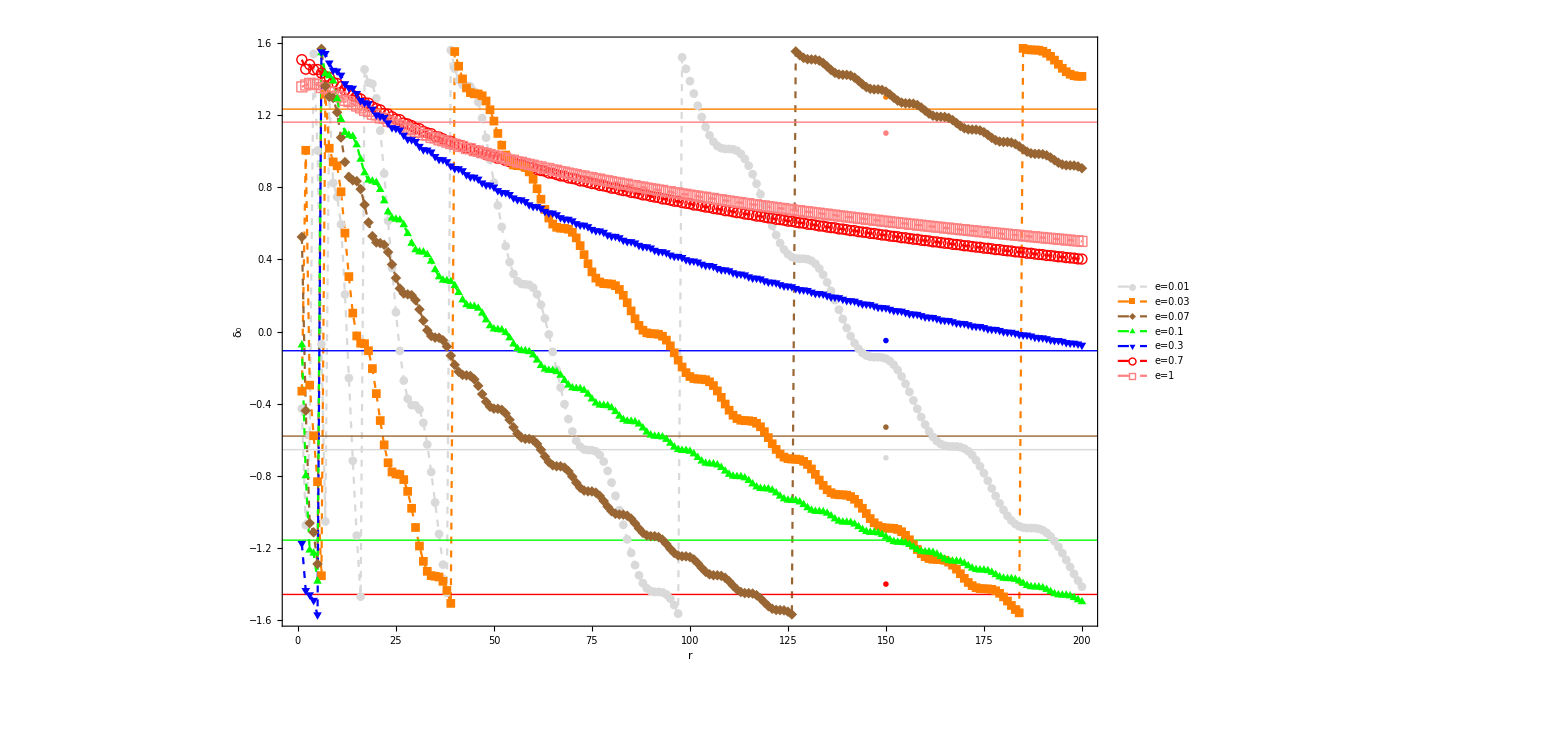

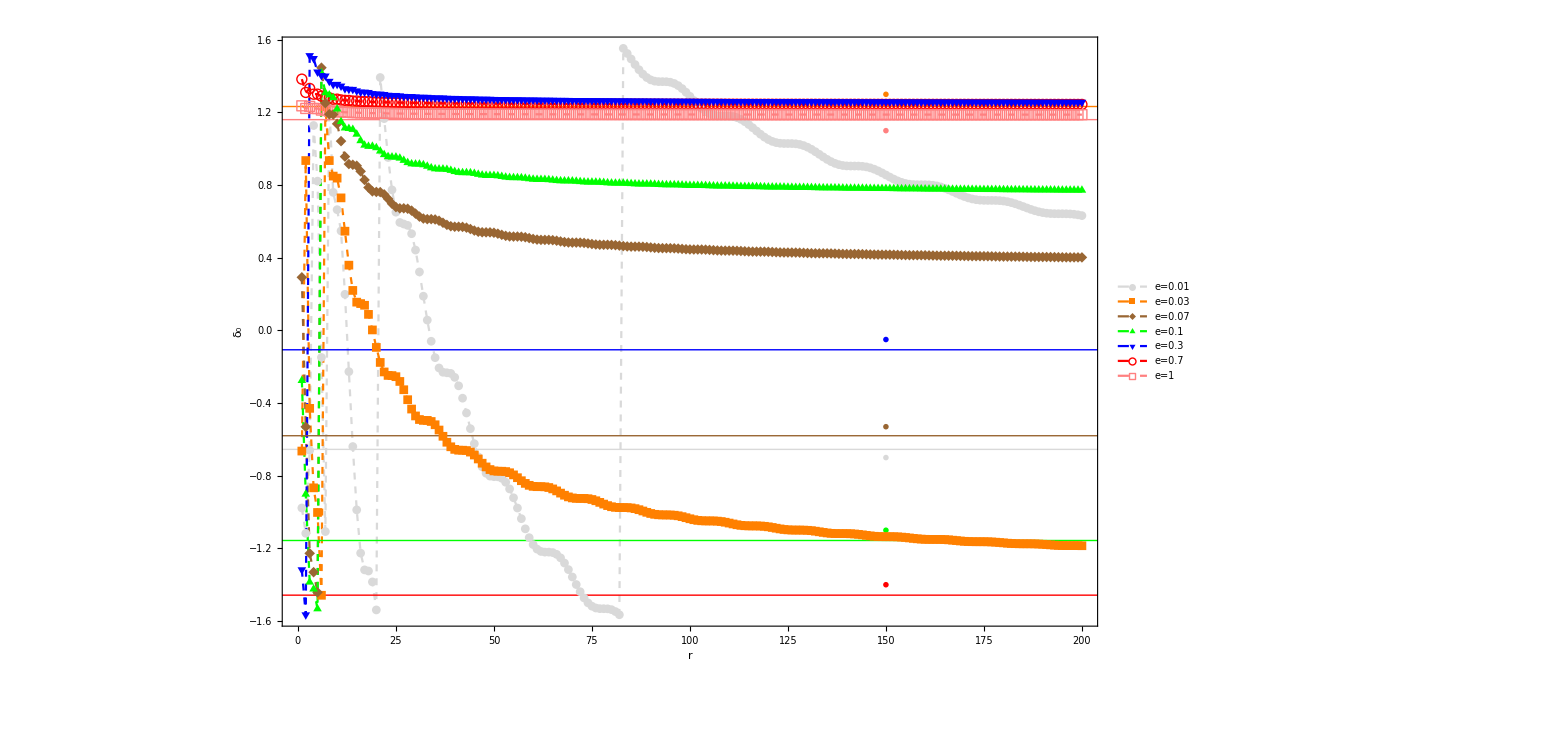

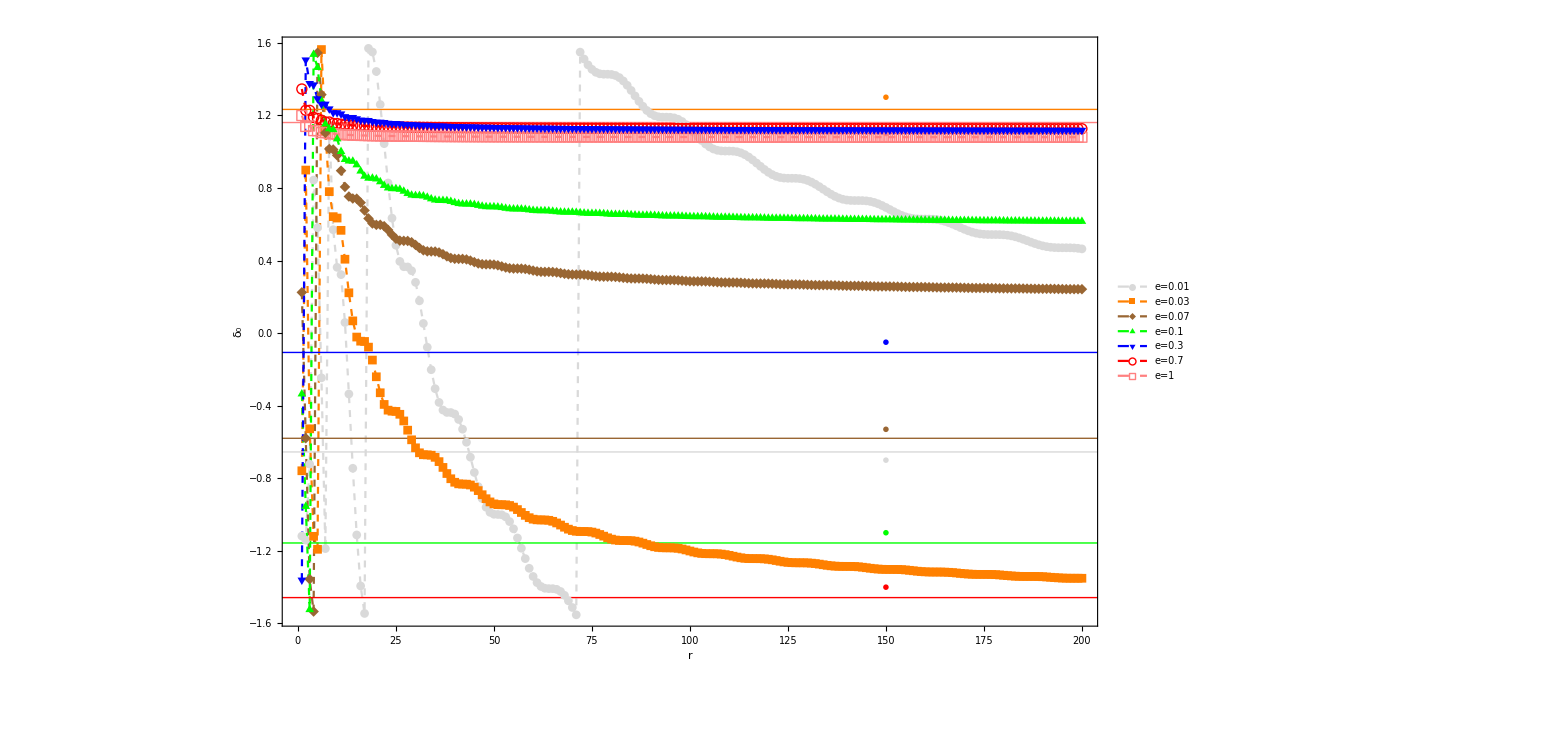

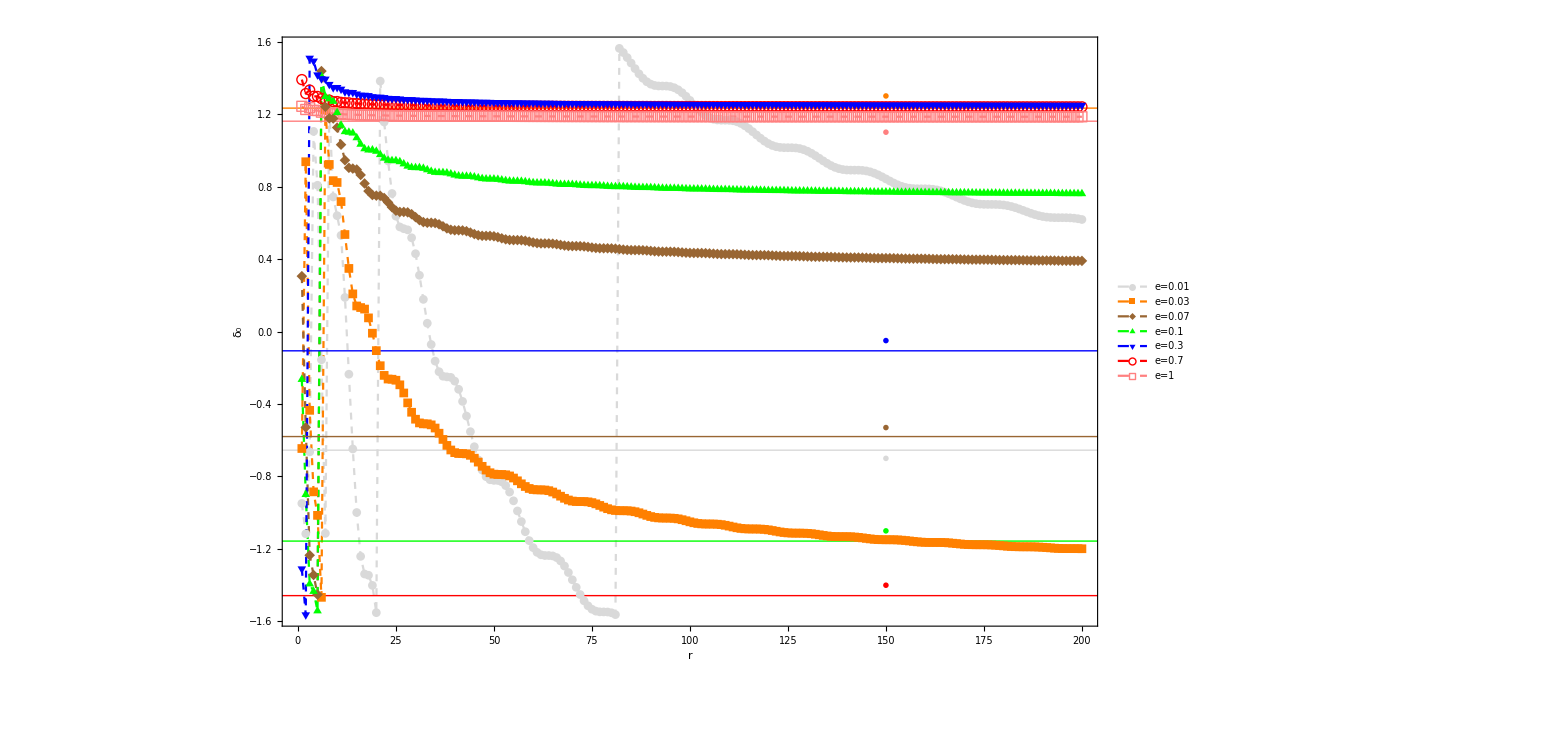

```mathematica
ListPlot[{SPS1,SPS2,SPS3,SPS4,SPS5,SPS6,SPS7},Frame->True,FrameTicks->{{All,None},{All,None}},Joined->True,PlotMarkers->Automatic,ImageSize->1200,FrameLabel->{"r","δ_0"},RotateLabel->False,PlotStyle->{{Dashed,LightGray,PointSize->Tiny},{Dashed,Orange,PointSize->Tiny},{Dashed,Brown,PointSize->Tiny},{Dashed,Green,PointSize->Tiny},{Dashed,Blue,PointSize->Tiny},{Dashed,Red,PointSize->Tiny},{Dashed,Pink,PointSize->Tiny}},Axes->None,Epilog->{{LightGray,Thin,InfiniteLine[{0,-0.654835316},{1,0}],Inset[Style["δ_0(e=0.01)=-0.654835316",14],{150,-0.7}]},{Orange,Thin,InfiniteLine[{0,1.232867297},{1,0}],Inset[Style["δ_0(e=0.03)=1.232867297",14],{150,1.3}]},{Brown,Thin,InfiniteLine[{0,-0.579619620},{1,0}],Inset[Style["δ_0(e=0.07)=-0.579619620",14],{150,-0.53}]},{Green,Thin,InfiniteLine[{0,-1.156444634},{1,0}],Inset[Style["δ_0(e=0.1)=-1.156444634",14],{150,-1.1}]},{Blue,Thin,InfiniteLine[{0,-0.106466466},{1,0}],Inset[Style["δ_0(e=0.3)=-0.106466466",14],{150,-0.05}]},{Red,Thin,InfiniteLine[{0,-1.457426179},{1,0}],Inset[Style["δ_0(e=0.7)=-1.457426179",14],{150,-1.4}]},{Pink,Thin,InfiniteLine[{0,1.160634967},{1,0}],Inset[Style["δ_0(e=1)=1.160634967",14],{150,1.1}]}},PlotLegends->{"e=0.01","e=0.03","e=0.07","e=0.1","e=0.3","e=0.7","e=1"}]
Export["C:\\Users\\ASUS\\OneDrive\\文档\\Test_6\\Test_PhaseShift_NA_ar^b_nor^-1.eps",%];
```

```mathematica
Unset[e];
N[1/(2I)Log[Gamma[1-I/(√(2#))]/Gamma[1+I/(√(2#))]]]&/@{0.01,0.03,0.07,0.1,0.3,0.7,1}
```

{-1.25044+5.55112×10^-17 ⅈ,0.716281+5.55112×10^-17 ⅈ,-0.708782+0. ⅈ,-0.311203+5.55112×10^-17 ⅈ,0.242033-5.55112×10^-17 ⅈ,0.306557+0. ⅈ,0.293923+0. ⅈ}

```mathematica
{-0.654835316,1.232867297,-0.579619620,-1.156444634,-0.106466466,-1.457426179,1.160634967}
```

{-0.654835,1.23287,-0.57962,-1.15644,-0.106466,-1.45743,1.16063}

```mathematica
%1-%3
```

```mathematica
{0.5956066894816177-5.551115123125783*^-17 ⅈ,0.5165865057729152-5.551115123125783*^-17 ⅈ,0.1291623302503362+0. ⅈ,-0.8452418156010307-5.551115123125783*^-17 ⅈ,-0.34849924048046027+5.551115123125783*^-17 ⅈ,1.3776094345459944+0. ⅈ,0.8667124317575183+0. ⅈ}
```

{0.595607-5.55112×10^-17 ⅈ,0.516587-5.55112×10^-17 ⅈ,0.129162+0. ⅈ,-0.845242-5.55112×10^-17 ⅈ,-0.348499+5.55112×10^-17 ⅈ,1.37761+0. ⅈ,0.866712+0. ⅈ}

```mathematica
-1.7639832190437987 +π
```

1.37761